```mathematica
U:1;D:2;F:3;B:4;L:5;R:6; The all transformation are as follows:
S1, S2, S3, S4, S5, S6, S7, S8, S9. The symbolic here is same as the notebook I had worked before, the symbol Si represents the transformation Subscript[S, i] in my work
```

```mathematica
S1={11->17,17->19,19->13,13->11,14->18,18->16,16->12,12->14,31->61,61->43,43->53,53->31,33->63,63->41,41->51,51->33,32->62,62->42,42->52,52->32};
S2={34->64,64->46,46->56,56->34,35->65,65->45,45->55,55->35,36->66,66->44,44->54,54->36};
S3={21->27,27->29,29->23,23->21,24->28,28->26,26->22,22->24,37->67,67->49,49->59,59->37,39->69,69->47,47->57,57->39,38->68,68->48,48->58,58->38};
S4={51->57,57->59,59->53,53->51,54->58,58->56,56->52,52->54,11->31,31->27,27->47,47->11,17->37,37->21,21->41,41->17,14->34,34->24,24->44,44->14};
S5={12->32,32->28,28->48,48->12,18->38,38->22,22->42,42->18,15->35,35->25,25->45,45->15};
S6={61->67,67->69,69->63,63->61,64->68,68->66,66->62,62->64,13->33,33->29,29->49,49->13,19->39,39->23,23->43,43->19,16->36,36->26,26->46,46->16};
S7={31->33,33->39,39->37,37->31,32->36,36->38,38->34,34->32,17->61,61->29,29->57,57->17,19->67,67->27,27->51,51->19,18->64,64->28,28->54,54->18};
S8={14->62,62->26,26->58,58->14,16->68,68->24,24->52,52->16,15->65,65->25,25->55,55->15};
S9={41->43,43->49,49->47,47->41,42->46,46->48,48->44,44->42,11->63,63->23,23->59,59->11,13->69,69->21,21->53,53->13,12->66,66->22,22->56,56->12};
StartSet={31,32,33,34,35,36,37,38,39,41,42,43,44,45,46,47,48,49,51,52,53,54,55,56,57,58,59,61,62,63,64,65,66,67,68,69,11,12,13,14,15,16,17,18,19,21,22,23,24,25,26,27,28,29};
```

```mathematica
The symbol ISi represents the Inverse transformation of Si, it is also stand for (Subscript[S, i]^-1).
```

```mathematica
IS1=Exch[{StartSet,StartSet/.S1/.S1/.S1}];
IS2=Exch[{StartSet,StartSet/.S2/.S2/.S2}];
IS3=Exch[{StartSet,StartSet/.S3/.S3/.S3}];
IS4=Exch[{StartSet,StartSet/.S4/.S4/.S4}];
IS5=Exch[{StartSet,StartSet/.S5/.S5/.S5}];
IS6=Exch[{StartSet,StartSet/.S6/.S6/.S6}];
IS7=Exch[{StartSet,StartSet/.S7/.S7/.S7}];
IS8=Exch[{StartSet,StartSet/.S8/.S8/.S8}];
IS9=Exch[{StartSet,StartSet/.S9/.S9/.S9}];
```

```mathematica
All transformations contained in the parameter prmt
prmt={Subscript[S, 1],Subscript[S, 2],Subscript[S, 3],Subscript[S, 4],Subscript[S, 5],Subscript[S, 6],Subscript[S, 7],Subscript[S, 8],Subscript[S, 9],Subscript[S, 1]^-1,Subscript[S, 2]^-1,Subscript[S, 3]^-1,Subscript[S, 4]^-1,Subscript[S, 5]^-1,Subscript[S, 6]^-1,Subscript[S, 7]^-1,Subscript[S, 8]^-1,Subscript[S, 9]^-1}
```

```mathematica
prmt(*mypermutation*)={S1,S2,S3,S4,S5,S6,S7,S8,S9,IS1,IS2,IS3,IS4,IS5,IS6,IS7,IS8,IS9};
```

```mathematica
Exch[list_]:=Module[{len=Length[list[[1]]],per={}},For[Exchi=1,Exchi≤Length[list[[1]]],Exchi++,If[list[[1,Exchi]]≠ list[[2,Exchi]],per=per∪{list[[1,Exchi]]->list[[2,Exchi]]}]];
per
];
```

```mathematica
Place[Lst_,Rndm_]:=Module[{tr={},p={}},tr=Array[Lst[[1,#2]]≥ Rndm>Sign[#2-1]Lst[[1,#2-1]]&,{1,18}];
p=Flatten[Position[tr[[1]],True],1];p[[1]]](*选择第p条路, Lst:{{...}}, Rndm: Num*)
AntTrace[Prbblt_,rndmst_,trnslng_]:=Module[{trc={}},AppendTo[trc,Place[{Prbblt[[1]]},rndmst[[1]]]];For[i=1,i≤trnslng-1,i++,AppendTo[trc,Place[{Prbblt[[2,i,Last[trc]]]},rndmst[[1+i]]]]];trc];(*返回蚂蚁的路径, Prbblt:{
{...},
{
{{...}...{...}},{...}...{...}
}
}, rndmst:{...}*)
Exch[list_]:=Module[{len=Length[list[[1]]],per={}},For[Exchi=1,Exchi≤Length[list[[1]]],Exchi++,If[list[[1,Exchi]]≠ list[[2,Exchi]],per=per∪{list[[1,Exchi]]->list[[2,Exchi]]}]];
per
];(*变换公式, List:{Start,End}*)
PermulateMultiply[Srtst_,List_]:=Module[{Cntr=Srtst,ndSt={}},For[i=1,i≤Length[List],i++,Cntr=Cntr/.prmt[[List[[i]]]]];ndSt=Exch[{StartSet,Cntr}]];(*Srtst:StartSet, List: AntTrace[...]*)
```

```mathematica
**********************************历史实验区
```

```mathematica
Exch[{{1,2,3,4},{2,3,1,4}}]
```

{1→2,2→3,3→1}

```mathematica
t={15,18,4,7};
PermulateMultiply[StartSet,t]
```

{11→53,12→52,13→43,14→32,16→42,17→31,18→64,19→61,21→69,22→66,23→37,24→44,26→38,27→47,28→54,29→39,31→51,32→36,33→19,34→24,36→16,37→21,38→34,39→67,41→11,42→14,43→63,44→48,46→26,47→49,48→46,49→57,51→17,52→18,53→41,54→58,56→22,57→59,58→56,59→23,61→33,62→12,63→13,64→62,66→68,67→29,68→28,69→27}

```mathematica
**********************************历史实验区
```

```mathematica
prbblt=Array[#2/18&,{1,18}];
AppendTo[prbblt,Table[Array[#2/18&,{18,18}],{i,8}]];
rndmst=RandomReal[1,9](*随机路径生成*)
Place[{prbblt[[1]]},rndmst[[1]]](*选择路径的函数示例*)
AntTrace[prbblt,rndmst,9](*使用蚂蚁轨迹的函数示例*)
trace=PermulateMultiply[StartSet,AntTrace[prbblt,rndmst,9]](*随机路径决定的变换结果*)
```

{0.143442,0.929304,0.362694,0.734891,0.973924,0.675751,0.342375,0.354512,0.697201}

3

{3,17,7,14,18,13,7,7,13}

{11→61,12→46,13→57,14→64,15→55,16→58,17→51,18→52,19→53,21→59,22→68,23→69,24→56,25→65,26→32,27→67,28→62,29→63,31→17,32→14,33→11,34→54,35→15,36→28,37→39,38→16,39→13,41→19,42→66,43→37,44→48,45→25,46→42,47→21,48→26,49→23,51→31,52→36,53→33,54→34,55→35,56→22,57→29,58→44,59→47,61→41,62→24,63→27,64→38,65→45,66→12,67→43,68→18,69→49}

```mathematica
**********************************主要函数定义
```

```mathematica
trnslng 是变换的个数, Lngthn 变换最短
```

```mathematica
Ant[Prbblt_,rndmst_,Lngthn_,trypic_,trnslng_]:=Module[{trace={},Trans={},p=0,x={},l=0,prbbl=Prbblt,kuosan=1/8192,mygraph={},releaseform={}},
trace=AntTrace[prbbl,rndmst,trnslng](*蚂蚁的轨迹*);Trans=PermulateMultiply[StartSet,trace];
l=Length[Trans];p=trace[[1]];If[l==0,l=50;Print["l=0,reset l=50"]];
x=Differences[Flatten[{0,prbbl[[1]]}]];x[[p]]+=2/l;x+=kuosan(*气味飘散*);
prbbl[[1]]=Accumulate[x/Total[x]];
For[i=1,i≤trnslng-1,i++,p=trace[[1+i]];x=Differences[Flatten[{0,prbbl[[2,i,trace[[i]]]]}]];x[[p]]+=2/l;x+=kuosan(*气味飘散*);prbbl[[2,i,trace[[i]]]]=Accumulate[x/Total[x]]];
releaseform=Table[If[trace[[i]]≤9,trace[[i]],-(trace[[i]]-9)],{i,trnslng}];(*书面形式处理*)
mygraph={Table[{i,trace[[i]]},{i,trnslng}]};(*mygraph=Flatten[AppendTo[mygraph,Table[{i,j},{j,18},{i,trnslng}]],1];*)

If[trypic==0∧Length[Trans]≤Lngthn,Print[Trans,"=",Style[Table[TraditionalForm[If[Sign[releaseform[[i]]]<0,Subsuperscript[S,Abs[releaseform[[i]]],-1],Subscript[S,releaseform[[i]]]]],{i,trnslng,1,-1}],24,Blue]]](*书面写法*);
If[trypic==1,Print[TreePlot[Trans,DirectedEdges-> True,AspectRatio->Automatic,VertexLabeling -> True,ImageSize->400]]];(*树形图*)
If[trypic==2,Print[ListLinePlot[mygraph,PlotMarkers->Automatic,Filling->{1->Axis},GridLines->{Table[i,{i,trnslng}],Table[i,{i,18}]},PlotRange->{{1,trnslng},{1,18}},ImageSize->400]]];(*路径图*)
If[trypic==3,Print[BarChart[{prbbl[[1]]}∪Table[prbbl[[2,ii,trace[[ii]]]],{ii,trnslng-1}],ImageSize->400]]];(*直方图*)
If[trypic==4,Print[ListLinePlot[{prbbl[[1]]}∪Table[ii/1.25 prbbl[[2,ii,trace[[ii]]]],{ii,trnslng-1}],ImageSize->400]]];(*概率的折线图*)
If[trypic==5∧Length[Trans]≤Lngthn,
Print[Trans,"=",Style[Table[TraditionalForm[If[Sign[releaseform[[i]]]<0,Subsuperscript[S,Abs[releaseform[[i]]],-1],Subscript[S,releaseform[[i]]]]],{i,trnslng,1,-1}],24,Blue]];
Print[TreePlot[Trans,DirectedEdges-> True,AspectRatio->Automatic,VertexLabeling -> True,ImageSize->400],
ListLinePlot[mygraph,PlotMarkers->Automatic,Filling->{1->Axis},GridLines->{Table[i,{i,trnslng}],Table[i,{i,18}]},PlotRange->{{1,trnslng},{1,18}},ImageSize->400],
BarChart[{prbbl[[1]]}∪Table[prbbl[[2,ii,trace[[ii]]]],{ii,trnslng-1}],ImageSize->400]]
];
If[trypic==6∧Length[Trans]≤Lngthn,
Print[Trans,"=",Style[Table[TraditionalForm[If[Sign[releaseform[[i]]]<0,Subsuperscript[S,Abs[releaseform[[i]]],-1],Subscript[S,releaseform[[i]]]]],{i,trnslng,1,-1}],24,Blue]];
Print[TreePlot[Trans,DirectedEdges-> True,AspectRatio->Automatic,VertexLabeling -> True,ImageSize->400],
ListLinePlot[mygraph,PlotMarkers->Automatic,Filling->{1->Axis},GridLines->{Table[i,{i,trnslng}],Table[i,{i,18}]},PlotRange->{{1,trnslng},{1,18}},ImageSize->400],
ListLinePlot[{prbbl[[1]]}∪Table[ii/1.25 prbbl[[2,ii,trace[[ii]]]],{ii,trnslng-1}],PlotMarkers->Automatic,ImageSize->400]]
];

{prbbl,Min[l,Lngthn]}]
```

```mathematica
------------------------------------历史实验区
```

```mathematica
(*概率空间的构造*)
prbblt=Array[#2/18&,{1,18}];
AppendTo[prbblt,Table[Array[#2/18&,{18,18}],{i,8}]];
(*prbblt[[1]]和prbblt[[2]], prbblt[[2]]有8个步, 每步18种已达到的路线, 每种路线有18种候选路线*)
translength=50;
times=1;
While[times<15,For[i=1,i≤3,i++,rndmst=RandomReal[1,9];{prbblt,translength}=Ant[prbblt,rndmst,translength,0,9]];times++]
```

{11→27,12→26,14→62,16→12,17→41,18→54,19→51,21→69,22→66,23→39,24→14,26→64,27→59,28→56,29→61,31→11,32→34,33→31,34→28,35→55,36→32,37→47,38→44,39→33,41→37,42→68,44→48,45→65,46→58,47→49,48→46,49→29,51→53,52→16,53→57,54→38,55→45,56→22,57→21,58→52,59→23,61→17,62→42,64→18,65→35,66→24,67→19,68→36,69→67},{18,1,6,11,7,4,4,15,16}

{11→63,12→44,13→33,16→66,19→69,21→57,22→26,23→29,24→58,26→28,27→59,28→34,29→53,33→23,34→48,37→47,38→54,39→41,41→43,42→56,43→19,44→12,46→62,47→37,48→68,49→67,53→13,54→22,56→42,57→21,58→24,59→27,61→49,62→46,63→61,66→16,67→11,68→38,69→39},{11,12,1,9,9,2,18,13,10}

```mathematica
////////////////////////////////////////////实验区
```

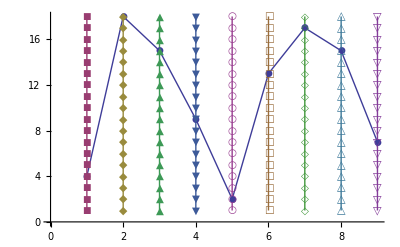

```mathematica
prbblt=Array[#2/18&,{1,18}];
AppendTo[prbblt,Table[Array[#2/18&,{18,18}],{i,8}]];(*概率空间*)
rndmst=RandomReal[1,9](*随机路径生成*);
trace=AntTrace[prbblt,rndmst,9];
ListLinePlot[{Table[{i,trace[[i]]},{i,9}]}∪Table[{i,j},{i,9},{j,18}],PlotMarkers->Automatic]
Trans=PermulateMultiply[StartSet,trace];
l=Length[Trans];

p=trace[[1]];
x=Differences[Flatten[{0,prbblt[[1]]}]];
x[[p]]+=10/l;
prbblt[[1]]=Accumulate[x/Total[x]];

For[i=1,i≤8,i++,p=trace[[1+i]];x=Differences[Flatten[{0,prbblt[[2,i,trace[[i]]]]}]];x[[p]]+=10/l;prbblt[[2,i,trace[[i]]]]=Accumulate[x/Total[x]];]
```

```mathematica
{prbblt[[1]]}∪Table[prbblt[[2,i,trace[[i]]]],{i,1}]
```

{{7/156,7/78,7/52,7/39,35/156,7/26,49/156,14/39,21/52,35/78,77/156,7/13,7/12,49/78,35/52,28/39,119/156,1},{7/156,7/78,7/52,29/78,5/12,6/13,79/156,43/78,31/52,25/39,107/156,19/26,121/156,32/39,45/52,71/78,149/156,1}}

```mathematica
////////////////////////////////////////////存档区
```

```mathematica
(*概率空间的构造*)
translength=7;(*变换次数*)
prbblt=Array[#2/18&,{1,18}];
AppendTo[prbblt,Table[Array[#2/18&,{18,18}],{i,translength-1}]];
prbblt=N[prbblt];
(*prbblt[[1]]和prbblt[[2]], prbblt[[2]]有8个步, 每步18种已达到的路线, 每种路线有18种候选路线*)
trnslngth=50;(*最终变换最初不超过50个长度*)
times=1;
While[trnslngth>10∧times<5000,rndmst=RandomReal[1,translength](*随机路径*);{prbblt,trnslngth}=Ant[prbblt,rndmst,trnslngth,6,translength];times++]
Print["End"]
```

$Aborted

End

```mathematica
Group
```

```mathematica
\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\实验进行区
```

{2012,7,21,23,3,58.5966796}

{21→27,22→24,23→21,24→28,26→22,27→29,28→26,29→23,37→67,38→68,39→69,47→57,48→58,49→59,57→39,58→38,59→37,67→49,68→48,69→47}={S_3,S_1^-1,S_1,S_1^-1,S_2^-1,S_1,S_4,S_4^-1,S_1^-1,S_2,S_2^-1,S_1,S_2}

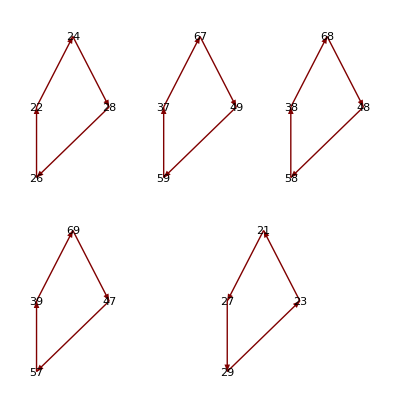
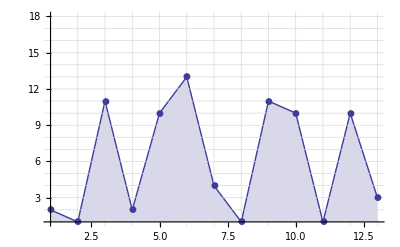
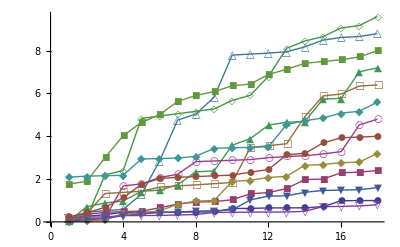

{11→31,14→64,17→37,21→41,24→44,27→47,31→27,36→58,37→21,41→17,44→14,47→11,51→57,52→36,53→51,56→52,57→59,58→56,59→53,64→24}={S_7,S_5^-1,S_9,S_9^-1,S_7^-1,S_6^-1,S_4,S_6,S_7,S_4,S_5,S_4^-1,S_7^-1}

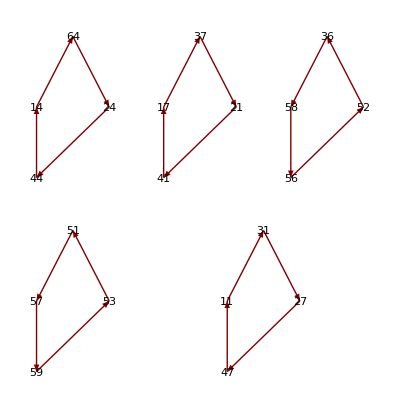
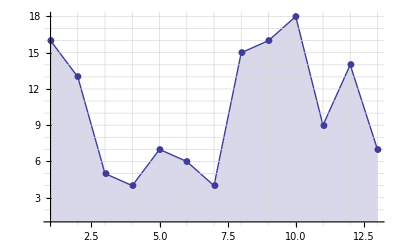
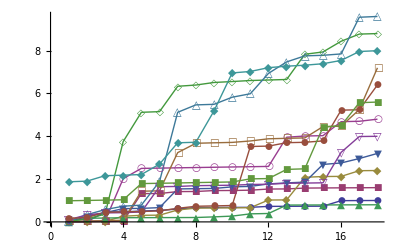

{12→32,15→55,18→38,22→42,25→65,28→48,32→28,38→22,42→18,48→12,55→25,65→15}={S_2^-1,S_4^-1,S_5^-1,S_4,S_5,S_2,S_3^-1,S_3,S_2^-1,S_5,S_2,S_8,S_8^-1}

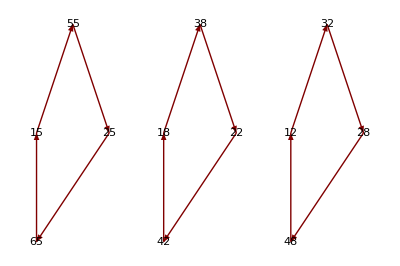
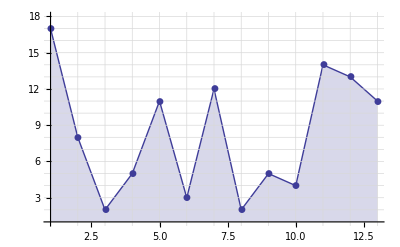
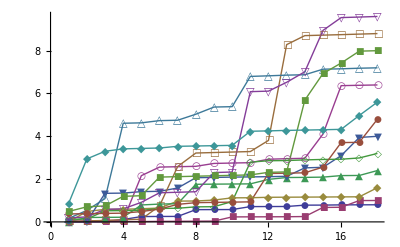

{14→62,15→65,16→68,24→52,25→55,26→58,52→16,55→15,58→14,62→26,65→25,68→24}={S_7^-1,S_7,S_5^-1,S_4,S_5,S_9^-1,S_1,S_1^-1,S_9,S_5^-1,S_5,S_4^-1,S_8}

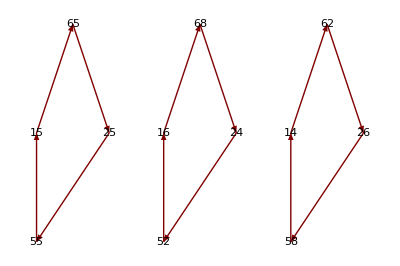
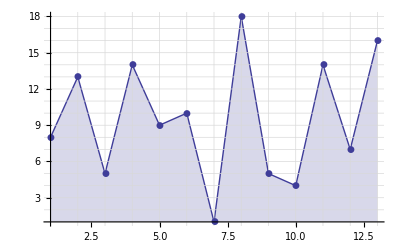
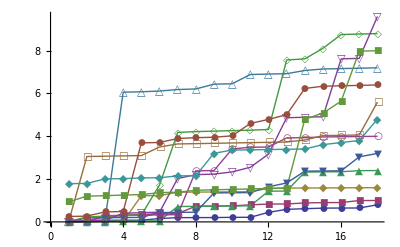

{12→38,15→65,18→42,22→32,25→55,28→48,32→12,38→22,42→28,48→18,55→15,65→25}={S_4,S_4^-1,S_1,S_8^-1,S_4^-1,S_4,S_7,S_8,S_7^-1,S_3^-1,S_8,S_3,S_1^-1}

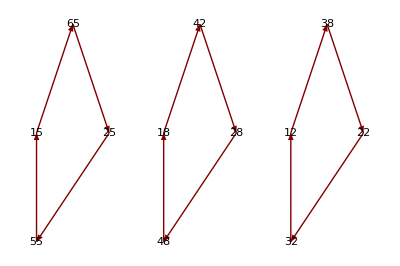
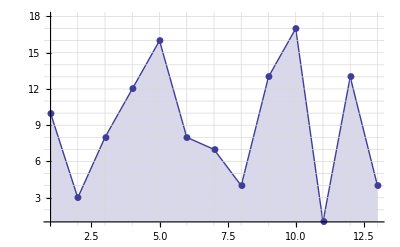
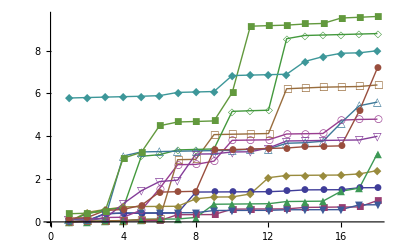

{14→38,15→45,16→52,22→62,25→35,28→48,35→15,38→22,45→25,48→16,52→28,62→14}={S_1^-1,S_2,S_2,S_5,S_2,S_1,S_3^-1,S_3,S_6,S_6^-1,S_2,S_2^-1,S_2}

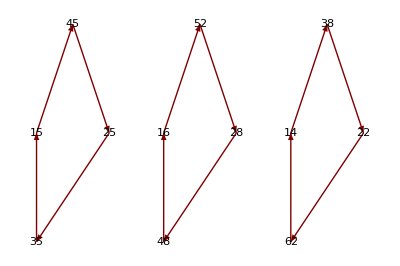
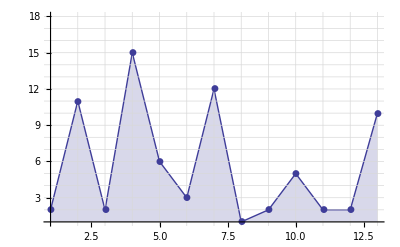
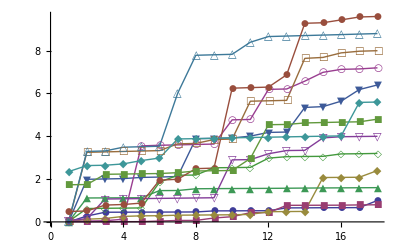

$Aborted

{2012,7,21,23,19,37.5664062}

```mathematica
(*概率空间的构造*)
translength=13;(*变换次数*)
prbblt=Array[#2/18&,{1,18}];
AppendTo[prbblt,Table[Array[#2/18&,{18,18}],{i,translength-1}]];
prbblt=N[prbblt];
(*prbblt[[1]]和prbblt[[2]], prbblt[[2]]有8个步, 每步18种已达到的路线, 每种路线有18种候选路线*)
trnslngth=20;(*最终变换最初不超过20个长度*)
times=AbsoluteTime[DateList[]];
DateList[]
While[trnslngth≥ 4∧AbsoluteTime[DateList[]]-times≤20*60,rndmst=RandomReal[1,translength](*随机路径*);{prbblt,trnslngth}=Ant[prbblt,rndmst,trnslngth,6,translength]]
DateList[]
```

{12→68,14→42,16→52,18→22,22→38,26→62,28→32,32→48,34→64,36→66,38→18,42→26,44→54,46→56,48→28,52→12,54→36,56→34,62→14,64→46,66→44,68→16},{16,7,17,10,2,8,2,1,11,14,2,7,16,11}

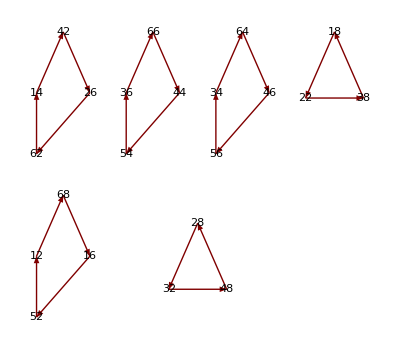
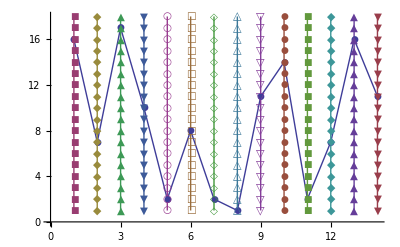
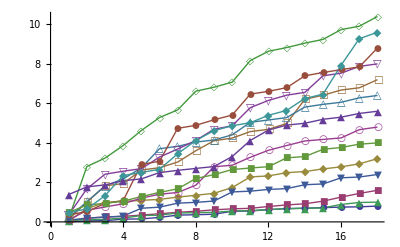

{12→52,14→12,15→35,18→38,22→18,24→68,25→45,26→22,28→34,32→28,34→58,35→55,36→66,38→54,42→14,44→36,45→65,46→56,48→32,52→42,54→24,55→15,56→64,58→26,64→46,65→25,66→44,68→48},{5,17,5,12,2,9,8,9,9,7,16,2,9,3}

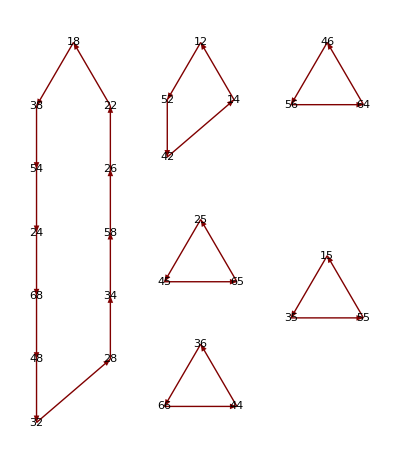
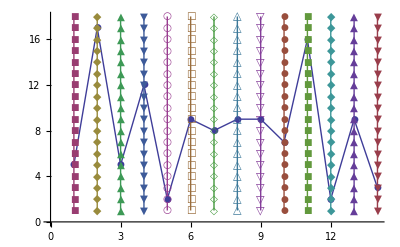
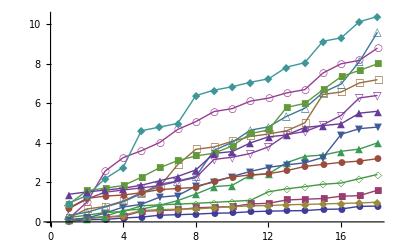

{12→22,14→28,16→68,17→27,18→24,19→69,22→64,23→33,24→18,26→56,27→17,28→14,31→57,32→58,33→23,34→42,36→34,37→51,38→52,42→48,44→66,46→62,48→36,49→61,51→37,52→38,54→12,56→46,57→31,58→32,61→49,62→26,64→54,66→16,68→44,69→19},{16,15,5,4,13,9,17,16,12,14,11,6,15,18}

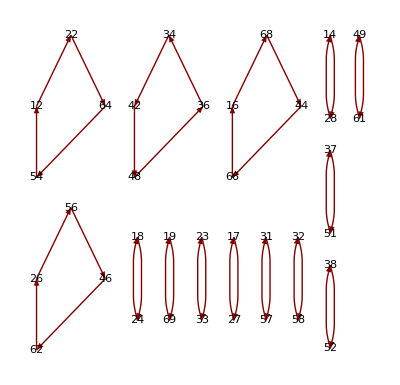
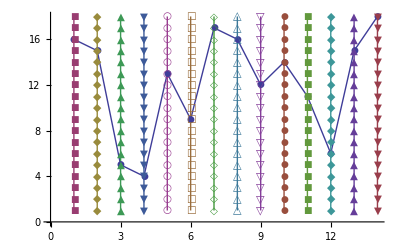
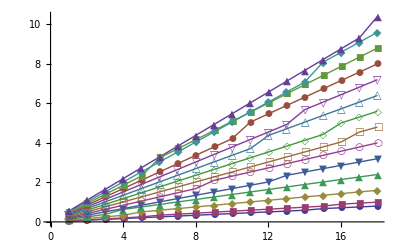

{14→26,15→25,16→24,24→16,25→15,26→14,52→68,55→65,58→62,62→58,65→55,68→52},{8,6,2,11,15,8,16,7}

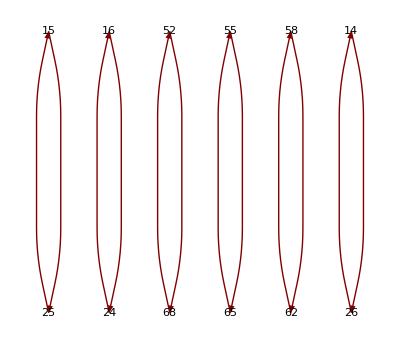
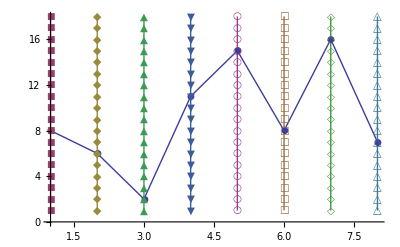
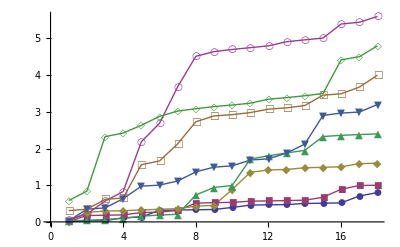

{11→57,14→38,17→39,24→34,27→31,28→58,29→11,31→67,34→14,37→17,38→24,39→53,41→27,51→29,52→28,53→37,54→52,57→51,58→54,67→41}={S_4,S_4,S_1^-1,S_1,S_7^-1,S_4^-1,S_7,S_4,S_4,S_6^-1,S_6,S_5^-1,S_5}

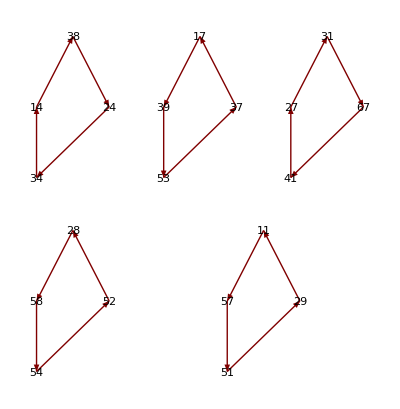
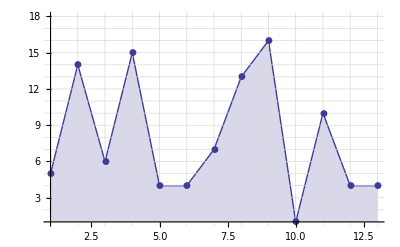
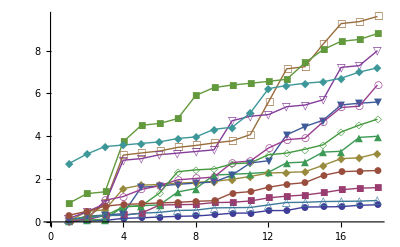

```mathematica
////////////////////////////////////////////////////最优结果存档区
```

```mathematica
//////////////////////////////////////////////////一个想法的验证
```

```mathematica
t={15,18,4,7};timet=1;
subset1={};
end=PermulateMultiply[StartSet,t]
PrependTo[end,1];
AppendTo[subset1,end]
```

{11→53,12→52,13→43,14→32,16→42,17→31,18→64,19→61,21→69,22→66,23→37,24→44,26→38,27→47,28→54,29→39,31→51,32→36,33→19,34→24,36→16,37→21,38→34,39→67,41→11,42→14,43→63,44→48,46→26,47→49,48→46,49→57,51→17,52→18,53→41,54→58,56→22,57→59,58→56,59→23,61→33,62→12,63→13,64→62,66→68,67→29,68→28,69→27}

{{1,11→53,12→52,13→43,14→32,16→42,17→31,18→64,19→61,21→69,22→66,23→37,24→44,26→38,27→47,28→54,29→39,31→51,32→36,33→19,34→24,36→16,37→21,38→34,39→67,41→11,42→14,43→63,44→48,46→26,47→49,48→46,49→57,51→17,52→18,53→41,54→58,56→22,57→59,58→56,59→23,61→33,62→12,63→13,64→62,66→68,67→29,68→28,69→27}}

```mathematica
t={15,18,4,7};timet=1;
subset1={};
end=PermulateMultiply[StartSet,t];
Print[TreePlot[end,DirectedEdges-> True,AspectRatio->Automatic,VertexLabeling -> True,ImageSize->400]]
PrependTo[end,timet];
AppendTo[subset1,end];
Print[end]
While[Length[end]≠1,t=Flatten[AppendTo[t,{15,18,4,7}]];end=PermulateMultiply[StartSet,t];Print[TreePlot[end,DirectedEdges-> True,AspectRatio->Automatic,VertexLabeling -> True,ImageSize->400]];timet++;PrependTo[end,timet];AppendTo[subset1,end];Print[end]]
```

```mathematica
t2={15,16,4,7};timet=1;
subset2={};
end=PermulateMultiply[StartSet,t2];
Print[TreePlot[end,DirectedEdges-> True,AspectRatio->Automatic,VertexLabeling -> True,ImageSize->400]]
PrependTo[end,timet];
AppendTo[subset2,end];
Print[end]
While[Length[end]≠1,t2=Flatten[AppendTo[t2,{15,16,4,7}]];end=PermulateMultiply[StartSet,t2];Print[TreePlot[end,DirectedEdges-> True,AspectRatio->Automatic,VertexLabeling -> True,ImageSize->400]];timet++;PrependTo[end,timet];AppendTo[subset2,end];Print[end]]
```

```mathematica
t3={15,17,4,7};timet=1;
subset3={};
end=PermulateMultiply[StartSet,t3];
Print[TreePlot[end,DirectedEdges-> True,AspectRatio->Automatic,VertexLabeling -> True,ImageSize->400]]
PrependTo[end,timet];
AppendTo[subset3,end];
Print[end]
While[Length[end]≠1,t3=Flatten[AppendTo[t3,{15,17,4,7}]];end=PermulateMultiply[StartSet,t3];Print[TreePlot[end,DirectedEdges-> True,AspectRatio->Automatic,VertexLabeling -> True,ImageSize->400]];timet++;PrependTo[end,timet];AppendTo[subset3,end];Print[end]]
```

```mathematica
t3={15,15,4,7};timet=1;
subset3={};
end=PermulateMultiply[StartSet,t3];
Print[TreePlot[end,DirectedEdges-> True,AspectRatio->Automatic,VertexLabeling -> True,ImageSize->400]]
PrependTo[end,timet];
AppendTo[subset3,end];
Print[end]
While[Length[end]≠1,t3=Flatten[AppendTo[t3,{15,15,4,7}]];end=PermulateMultiply[StartSet,t3];Print[TreePlot[end,DirectedEdges-> True,AspectRatio->Automatic,VertexLabeling -> True,ImageSize->400]];timet++;PrependTo[end,timet];AppendTo[subset3,end];Print[end]]
```

```mathematica
For[itr=1,itr≤9,itr++,
For[jtr=1,jtr≤9,jtr++,et={1,9,itr,jtr,10,18,itr+9,jtr+9};Print["et=",et];timet=1;t3=et;
subset3={};
end=PermulateMultiply[StartSet,t3];
If[Length[end]≤15,Print[TreePlot[end,DirectedEdges-> True,AspectRatio->Automatic,VertexLabeling -> True,ImageSize->400]]];
PrependTo[end,timet];
AppendTo[subset3,end];
If[Length[end]≤16,Print[end]];
While[Length[end]≠1&&timet<7,t3=Flatten[AppendTo[t3,et]];end=PermulateMultiply[StartSet,t3];If[Length[end]≤15,Print[TreePlot[end,DirectedEdges-> True,AspectRatio->Automatic,VertexLabeling -> True,ImageSize->400]]];timet++;PrependTo[end,timet];AppendTo[subset3,end];If[Length[end]≤16,Print[end]]]
]
]
```